### Use non-integer vecB for generating SLM patterns

```mathematica
patterntabArb[vecA_, period_, onfrac_,phaseInd_,phaseOffset_:0.,nphases_:5,sizex_:1280,sizey_:1024]:=(veckA={1,-1}Reverse[vecA];vecB=veckA/Norm[vecA]*period;area=vecB.veckA;onpix=area * onfrac;phaseStep=vecB/nphases;
Table[If[Mod[({x,y}-(phaseStep*phaseInd+phaseOffset/(2π)*vecB)).veckA,area]≥onpix,0,1],{y,0,sizey-1},{x,0,sizex-1}])
```

```mathematica
Animate[ArrayPlot[patterntabArb[{12,-1},6.28,.5,pI,π,5,128,128],Mesh->Automatic,DataReversed->True,ImageSize->Full],{pI,0,4,1},AnimationRate->2,AnimationRunning->False]
```

```mathematica
Animate[ArrayPlot[patterntabArb[{5,-11},4.802, .3,pI,π,5,128,128],Mesh->Automatic,DataReversed->True],{pI,0,4,1},AnimationRate->2,AnimationRunning->False]
```

```mathematica
Animate[ArrayPlot[patterntabArb[{-7,-10},4.801,.3,pI,0,5,128,128],Mesh->Automatic,DataReversed->True],{pI,0,4,1},AnimationRate->2,AnimationRunning->False]
```

### To find out the exact line spacing and phase steps in the patterns obtained from above

#### this function returns the line spacing (in pixels) and the absolute phase as a list:

```mathematica
patternProperties[vecA_, period_, onfrac_, phase_,phaseOffset_:0.,nphases_:5, sizex_:1280,sizey_:1024]:=
(pat=patterntabArb[vecA,period, onfrac,phase,phaseOffset,nphases,sizex,sizey];
minDim=Min[sizex,sizey];
fft=Fourier[Take[pat,minDim,minDim]];
angle=ArcTan[-vecA[[1]]/vecA[[2]]];
peak=Round[minDim/(period /{Sin[angle],Cos[angle]})];peakadjust=If[#>0,1,0]& /@peak;
peak+= peakadjust;(* because indexing starts at 1 and -1*)
tofit=Table[{x,Abs[fft[[##]]&@@({x,0}+peak)]},{x,-1,1}];fy=Fit[tofit,{1,x,x^2},x];dy=First[FindArgMax[fy,x]];tofit=Table[{x,Abs[fft[[##]]&@@({0,x}+peak)]},{x,-1,1}];fx=Fit[tofit,{1,x,x^2},x];dx=First[FindArgMax[fx,x]];precisepeak=peak+{dy,dx}-peakadjust;(* -peakadjust because indexing starts at 1 and -1*)
preciseangle=ArcTan[precisepeak[[1]]/precisepeak[[2]]];
{minDim/precisepeak[[1]]*Sin[preciseangle],Arg[fft[[##]]& @@peak]})
```

```mathematica
EvaluatePatternSet[vecA_, period_, targetPeriod_,onfrac_,nphases_:5]:=(results=Table[0,{y,1,nphases},{x,1,2}];For[i=0,i<nphases,i++,results[[i+1]]=patternProperties[vecA,period, onfrac,nphases-1-i,0.,nphases]];{results[[All,1]],StringJoin[ToString[#],"%"]&/@((results[[All,1]]-targetPeriod)/targetPeriod*100),If[#<-π,2π+#,#]&/@(results[[All,2]]-RotateRight[results[[All,2]],1])*180/π})
```

#### The first row shows the pattern’s line spacing, second row shows the relative error wrt the target line spacing, and the third the absolute phases

```mathematica
EvaluatePatternSet[{12,-1}, 5.53927,5.54556,0.5,3]//MatrixForm
```

(5.5455 | 5.5455 | 5.5455
-0.00110066% | -0.00107604% | -0.00109345%
120.003 | 119.991 | 120.006)

```mathematica
.488/2/.169
```

```mathematica
1.4437869822485208
5.51/1.14203
```

1.44379

```mathematica
4.8247419069551585
1.7/1.49
```

4.82474

1.14094

#### Fine-tune the SLM pattern period

```mathematica
PeriodError[vecA_, period_, onfrac_,TargetPeriod_,nphases_:5,sizex_:1280,sizey_:1024]:=(For[i=0,i<5,i++,results[[i+1]]=patternProperties[vecA,period,onfrac,4-i,nphases,sizex,sizey];];
Mean[Abs[(results[[All,1]]-TargetPeriod)/TargetPeriod]]*100)
```

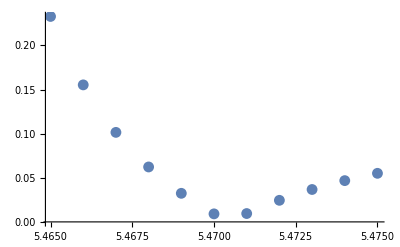

```mathematica
ListPlot[Table[{phase,PeriodError[{-7,-10},phase, 0.5,5.48]},{phase,5.465, 5.475,0.001}]]
```

### Write out generated patterns into 1-bit BMP files

```mathematica
For[i=0,i<3,i++,pat0=patterntabArb[{12,-1},4.8277, 0.5,i,0.,3];Export[StringJoin["pat-4.83256pixel-0.5DC-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<3,i++,pat0=patterntabArb[{5,-11},4.839, 0.5,i,0.,3];Export[StringJoin["pat-4.83256pixel-0.5DC-Ang1Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<3,i++,pat0=patterntabArb[{-7,-10},4.834, 0.5,i,0.,3];Export[StringJoin["pat-4.83256pixel-0.5DC-Ang2Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<3,i++,pat0=patterntabArb[{12,-1}, 5.53927, 0.5,i,0.,3];Export[StringJoin["pat-5.54556pixel-0.5DC-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<3,i++,pat0=patterntabArb[{5,-11},5.53925, 0.5,i,0.,3];Export[StringJoin["pat-5.54556pixel-0.5DC-Ang1Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<3,i++,pat0=patterntabArb[{-7,-10},5.5406, 0.5,i,0.,3];Export[StringJoin["pat-5.54556pixel-0.5DC-Ang2Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{12,-1},7.2185, 0.3,4-i];Export[StringJoin["pat-560nm-3DSIM100x-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{5,-11},7.241, 0.3,4-i];Export[StringJoin["pat-560nm-3DSIM100x-Ang1Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{-7,-10},7.214, 0.3,4-i];Export[StringJoin["pat-560nm-3DSIM100x-Ang2Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{12,-1},3.97995, 0.3,4-i];Export[StringJoin["pat-405nm-3DSIM-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{5,-11},3.98015, 0.3,4-i];Export[StringJoin["pat-405nm-3DSIM-Ang1Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{-7,-10},3.984, 0.3,4-i];Export[StringJoin["pat-405nm-3DSIM-Ang2Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{12,-1},5.0616, 0.3,4-i];Export[StringJoin["pat-514nm-3DSIM-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{5,-11},5.053, 0.3,4-i];Export[StringJoin["pat-514nm-3DSIM-Ang1Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{-7,-10},5.052, 0.3,4-i];Export[StringJoin["pat-514nm-3DSIM-Ang2Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{12,-1},4.3725, 0.3,4-i];Export[StringJoin["pat-445nm-3DSIM-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{5,-11},4.3826, 0.3,4-i];Export[StringJoin["pat-445nm-3DSIM-Ang1Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{-7,-10},4.3790, 0.3,4-i];Export[StringJoin["pat-445nm-3DSIM-Ang2Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{12,-1},5.7864, 0.3,4-i];Export[StringJoin["pat-589nm-3DSIM-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{5,-11},5.7975, 0.3,4-i];Export[StringJoin["pat-589nm-3DSIM-Ang1Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{-7,-10},5.7939, 0.3,4-i];Export[StringJoin["pat-589nm-3DSIM-Ang2Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{12,-1},5.2275, 0.3,4-i];Export[StringJoin["pat-532nm-3DSIM-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{5,-11},5.2264, 0.3,4-i];Export[StringJoin["pat-532nm-3DSIM-Ang1Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{-7,-10},5.2274, 0.3,4-i];Export[StringJoin["pat-532nm-3DSIM-Ang2Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{12,-1},6.3178, 0.3,4-i];Export[StringJoin["pat-642nm-3DSIM-Ang0Ph",ToString[i],".bmp"],Image[pat0, "Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{5,-11},6.3185, 0.3,4-i];Export[StringJoin["pat-642nm-3DSIM-Ang1Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
For[i=0,i<5,i++,pat0=patterntabArb[{-7,-10},6.3254, 0.3,4-i];Export[StringJoin["pat-642nm-3DSIM-Ang2Ph",ToString[i],".bmp"],Image[pat0,"Bit"], "BMP"]]
```

```mathematica
Image[patterntabArb[{0,10},6, .5,0,5,384,384]]
```

```mathematica
Image[patterntabArb[{5,-11},5,.5,0,5,256,256]]
```

```mathematica
{Image[patterntabArb[{0,10},4, .5,0,5,256,256]*patterntabArb[{Cos[#],Sin[#]}*12,4,.5,0,5,256,256]],Image[patterntabArb[{Cos[#],Sin[#]}*12,4,.5,0,5,256,256]]}&@(1.3)
```

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Moirepattern[a_,peroid_,size_]:=Image[patterntabArb[{0,10},peroid, .5,0,5,size,size]*patterntabArb[{Cos[a],Sin[a]}*12,peroid,.5,0,5,size,size]]
```

```mathematica
Manipulate[Moirepattern[a,6,384],{a,1.3,1.84}]
```

```mathematica
frames=Table[Moirepattern[a,6,384],{a,1.3,1.84,.05}]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Export["moirepattern.gif", frames]
```

moirepattern.gif

```mathematica
illumframes=Table[Image[patterntabArb[{Cos[a],Sin[a]}*12,6,.5,0,5,384,384]],{a,1.3,1.84,.05}]
```